# (* Definitions *)

```mathematica
(* This block defines all the necessary routines.  Run this, then check out some examples after it. *)

Clear[ri,c2,c4,getFourthOrderKE,getSecondOrderKE,getWH,getvH,getvHpoint,getRnl,getRnlpoint,getWxcNLR,getvxcNLRdirectpoint,SphereIntegrate,n]

(* Some defaults *)

(* guess for Subscript[R, NL] at the origin *)
guessR0=1; 

(* BuildSpline parameters *)
(* tolerance to get functions within to (at any given point) by using a refined spline.  you will probably get better than this (see the BuildSpline function), but it's a start. *)
FUNCTIONtolerance=10*^-6;  (*NOT RECOMMENDED TO BE OR GO BELOW 10*^-7 *)
(* if x coordinates in building a spline are smaller than this, skip ahead *)
TOOsmallDELTArSPLINE=10*^-5;

(* whether to debug (print lots of stuff) or not *)
DEBUG=False;
SUPERdebug=False;

(* occupation of s/p orbitals *)
soccupy={2};
poccupy={};


(* Debugging *)
(* printing indent level *)
INDENT="";

(* this prints something temporary if in debug mode, and permanent if in SUPERdebug *)
PrintPermanentSUPERdebug[string_]:=If[SUPERdebug,Print[INDENT<>string],If[DEBUG,PrintTemporary[INDENT<>string]]]

(* this prints something temporary if not in debug mode, and permanent if in debug *)
PrintPermanentDEBUG[string_]:=If[DEBUG,Print[INDENT<>string],PrintTemporary[INDENT<>string]]

(* this prints only if in debug mode *)
PrintOnlyDEBUG[string_]:=If[DEBUG,Print[INDENT<>string]]


(* Definition of the grid *)
(* points follow a slowly increasing radial grid *)

ri[i_]:=i GRIDdelta + MULTIPLIER GRIDdelta(i-1)i/2
GRIDmin:=ri[1]
GRIDmax:=ri[Ngrid]

Δrip[i_]:=ri[i+1]-ri[i]//Simplify
Δrim[i_]:=Δrip[i-1]
(* sparse grid *)
sparseri[i_]:=i SPARSEGRIDdelta + SPARSEmultiplier SPARSEGRIDdelta(i-1)i/2

(* in table form *)
rTABLE:=Table[ri[i],{i,1,Ngrid}]
ΔTABLE:=Table[1/2(Δrip[i]+Δrim[i]),{i,1,Ngrid}]
(* zero is in the sparse grid *)
SPARSErTABLE:=Join[{0},Table[sparseri[i],{i,1,SPARSENgrid}]] 


(* Kinetic energy pieces *)

(* Second-order finite-differences *)

c2[i_]:=(-1/2){(-4+2 (2+MULTIPLIER (-3+i)) i)/((1+MULTIPLIER (-1+i)) (2+MULTIPLIER (-1+i)) i (2+MULTIPLIER (-1+2 i)) GRIDdelta^2),(-4 i+2 MULTIPLIER (2+i-i^2))/((1+MULTIPLIER (-1+i)) (2+MULTIPLIER (-1+i)) i (1+MULTIPLIER i) GRIDdelta^2),(2 (2 (1+i)+MULTIPLIER (-2+i+i^2)))/((2+MULTIPLIER (-1+i)) i (1+MULTIPLIER i) (2+MULTIPLIER (-1+2 i)) GRIDdelta^2)}

getSecondOrderKE:=(
KE=Table[0,{i,1,Ngrid},{j,1,Ngrid}];

(* How to get laplacian at Subscript[r, 1], f1=f[Subscript[r, 1]]. *)
f0=f1-GRIDdelta(   (  (f2-f1)/(GRIDdelta(1+MULTIPLIER))  )    );  (*assume f0=f[Subscript[r, 0] = 0], can be extrapolated linearly to, using f[Subscript[r, 1]] = f1 and f2 = f[Subscript[r, 2]] *)
(* use second order formula and insert f0 as a function of f1 and f2*)
KE2i=c2[1].{f0,f1,f2}//Simplify;

KE[[1,1]]=Coefficient[KE2i,f1];
KE[[1,2]]=Coefficient[KE2i,f2];

(* IGNORE KE[[1,1;;2]] *)
For[i=2,i≤Ngrid,i++,
KE2ic=c2[i];
For[j=1,j≤Length[KE2ic],j++,
If[i-2+j≤Ngrid,
KE[[i,i-2+j]]=KE2ic[[j]];
]
]
];

KE
)

(* Fourth-order finite-differences *)

c4[i_]:=(-1/2){-(-4+2 i+MULTIPLIER (2+i (-19+5 i)+MULTIPLIER^2 i (3+i (4+(-8+i) i))+MULTIPLIER (2+i (5+i (-23+4 i)))))/(3 (1+MULTIPLIER (-2+i)) (1+MULTIPLIER (-1+i)) (2+MULTIPLIER (-1+i)) i (2+MULTIPLIER (-3+2 i)) (2+MULTIPLIER (-1+2 i)) GRIDdelta^2),(16 (-1+i)+8 MULTIPLIER (-2+i) (-1+5 i)+2 MULTIPLIER^3 i (9+i (13+4 (-5+i) i))+4 MULTIPLIER^2 (3+i (9+4 i (-7+2 i))))/(3 (1+MULTIPLIER (-2+i)) (1+MULTIPLIER (-1+i)) (2+MULTIPLIER (-1+i)) i (1+MULTIPLIER i) (2+MULTIPLIER (-1+2 i)) GRIDdelta^2),(-20 i+2 MULTIPLIER (16+5 (3-5 i) i+MULTIPLIER (-16+i (41+5 (5-4 i) i))+MULTIPLIER^2 (-6-(-1+i) i (-23+5 (-1+i) i))))/((1+MULTIPLIER (-1+i)) (2+MULTIPLIER (-1+i)) i (1+MULTIPLIER i) (2+MULTIPLIER+2 MULTIPLIER i) (2+MULTIPLIER (-3+2 i)) GRIDdelta^2),(16 (1+i)+8 MULTIPLIER (-4+5 i (1+i))+4 MULTIPLIER^2 (1+i (-23+8 i (1+i)))+2 MULTIPLIER^3 (6+i (9+i (-23+4 i (1+i)))))/(3 (1+MULTIPLIER (-1+i)) (2+MULTIPLIER (-1+i)) i (1+MULTIPLIER i) (1+MULTIPLIER+MULTIPLIER i) (2+MULTIPLIER (-1+2 i)) GRIDdelta^2),(-2 (2+i)+MULTIPLIER (10-i (13+5 i)-MULTIPLIER^2 (-1+i) i (-9+i (5+i))-MULTIPLIER (6+i (-27+i (13+4 i)))))/(3 (2+MULTIPLIER (-1+i)) i (1+MULTIPLIER i) (1+MULTIPLIER+MULTIPLIER i) (2+MULTIPLIER+2 MULTIPLIER i) (2+MULTIPLIER (-1+2 i)) GRIDdelta^2)}

getFourthOrderKE:=(
KE=Table[0,{i,1,Ngrid},{j,1,Ngrid}];

(* How to get laplacian at Subscript[r, 1], f1=f[Subscript[r, 1]]. *)
f0=f1-GRIDdelta(   (  (f2-f1)/(GRIDdelta(1+MULTIPLIER))  )    );  (*assume f0=f[Subscript[r, 0] = 0], can be extrapolated linearly to, using f[Subscript[r, 1]] = f1 and f2 = f[Subscript[r, 2]] *)
(* use second order formula and insert f0 as a function of f1 and f2*)
KE2i=c2[1].{f0,f1,f2}//Simplify;

KE[[1,1]]=Coefficient[KE2i,f1];
KE[[1,2]]=Coefficient[KE2i,f2];

(* second order KE at Subscript[r, 2] *)
KE2ic=c2[2];
For[j=1,j≤Length[KE2ic],j++,
If[j≤Ngrid,
KE[[2,j]]=KE2ic[[j]];
]
];

(* fourth order KE everywhere else *)
For[i=3,i≤Ngrid,i++,
KE4ic=c4[i];
For[j=1,j≤Length[KE4ic],j++,
If[i-3+j≤Ngrid,
KE[[i,i-3+j]]=KE4ic[[j]];
]
]
];

KE
)


(* General purpose - Spline builder *)


BuildSpline[f_]:=(
(* BuildSpline starts with a coarse grid and tests points off the grid, sees if the tolerance (FUNCTIONtolerance) is ok, and if not, adds another test point. *)
Module[{data,interpolation,i},
PrintPermanentDEBUG["first function pass through sparse grid"];
data=Monitor[Table[{r,f[r]},{r,sparsertable}],r];
interpolation=Interpolation[data,Method->"Spline"];
i=2;
PrintPermanentDEBUG["now refining grid for spline"];
Monitor[
While[i≤Length[data],
If[Abs[data[[i,1]]-data[[i-1,1]]]<TOOsmallDELTArSPLINE,
i+=2,
If[data[[i-1,1]]<10*^-12,
(* first x coordinate is zero, do something to average with second coordinate*)
newpoint=data[[i,1]]^(3/2),
(* x coordinate is not zero, harmonic average to weight towards smaller r *)
newpoint=2/(1/data[[i,1]]+1/data[[i-1,1]])
];
fnewpoint=f[newpoint];
(* no matter what, add in the new point and make a new interpolation *)
data=Join[data[[;;i-1]],{{newpoint,fnewpoint}},data[[i;;]]];
PrintPermanentSUPERdebug["   test r = "<>ToString[newpoint,FormatType->StandardForm]<>"; f(r) = "<>ToString[fnewpoint,FormatType->StandardForm]<>"; interp(r) = "<>ToString[interpolation[newpoint],FormatType->StandardForm]];
(* but only move up in i if the interpolation was a good approximation *)
If[Abs[fnewpoint-interpolation[newpoint]]<FUNCTIONtolerance,i+=2];
interpolation=Interpolation[data,Method->"Spline"];
]
],
(* have Monitor monitor the newpoint in r *)
newpoint
];
PrintPermanentDEBUG["amount of data in spline: "<>ToString[Length[data]]];
interpolation
]
)

(* Nonlocal integrators / nonlocal radius *)

SphereIntegrate[f_,r_,R_]:=(
(* integrate over r':
f[r'] in a sphere of radius R concentric with a point at
distance r from the origin *)
If[R<10*^-12,
0,
If[R>r,
If[r<10*^-12,
NIntegrate[4 Pi rp^2 f[rp], {rp,0,R}],
NIntegrate[4 Pi rp^2 f[rp], {rp,0,R-r}]+NIntegrate[Pi rp/r (R^2 - (r-rp)^2) f[rp], {rp,R-r,R+r}]
],
NIntegrate[Pi rp/r (R^2 - (r-rp)^2) f[rp], {rp,r-R,r+R}]
]
]
)

(* initial guess for Rnl *)
Rnl=Function[r,(guessR0+0.6r^(3/2)+r^3)/(1+r^2)];

getRnlpoint[r_]:=(
(* can get Rnl at a point, suspecting the point given by existing Rnl *)
Module[{R,func},
func[R_]:=If[R<0,R,SphereIntegrate[n,r,R]];
sol=Quiet[FindRoot[func[R]==1,{R,Rnl[r]}]];
R/.sol
]
)

getRnl:=(PrintPermanentDEBUG["Calculating NL radius..."];
INDENT=INDENT<>"   ";
Rnl=BuildSpline[getRnlpoint];
INDENT=StringDrop[INDENT,-3];
Rnl
)

BackNLRSphereIntegrate[f_,r_]:=(
(* integrate over r':
f[r'] if r is within a sphere of radius R(r') concentric with a point at position r' *)
Module[{R},
If[r<10*^-12,
(* if r is zero *)
NIntegrate[(R=Rnl[rp];
Piecewise[{{0,R<rp}},4 Pi rp^2])f[rp],{rp,0,MAXr}],
(* if r is nonzero *)
NIntegrate[(R=Rnl[rp];
Piecewise[{{0,R<Abs[r-rp]},
{1/r π rp (R^2-(r-rp)^2),R<r+rp}},
(4 Pi rp^2)])f[rp],{rp,0,MAXr}]
]
]
)


(* Hxc potentials and energies *)

(* HARTREE PIECES OF THINGS *)
getvHpoint[r_]:=If[r<10*^-12,
NIntegrate[4 π (rp) n[rp],{rp,0,MAXr}],
NIntegrate[(2 π (r+rp-Abs[r-rp]))/r(rp) n[rp],{rp,0,MAXr}]
]
getvH:=(PrintPermanentDEBUG["CALCULATING vH..."];
INDENT=INDENT<>"   ";
vH=BuildSpline[getvHpoint];
INDENT=StringDrop[INDENT,-3];
vH)

getWH:=(
PrintPermanentDEBUG["CALCULATING WH, via vH..."];
INDENT=INDENT<>"   ";
vH=getvH;
INDENT=StringDrop[INDENT,-3];
WH=NIntegrate[(4 Pi r^2) 1/2 vH[r] n[r],{r,0,MAXr}]
)

(* NLR XC PIECES *)
getvxcNLRdirectpoint[r_]:=(Module[{R},
R=Rnl[r];
(* integrate over r':  -1/2n[r']/|r-r'| in a sphere of radius R(r) concentric with a point at
distance r from the origin *)
(-1/2)If[R<10*^-12,
0,
If[R>r,
If[r<10*^-12,
NIntegrate[4Pi rp n[rp], {rp,0,R}],
NIntegrate[1/r 2 π rp (r+rp-Abs[r-rp]) n[rp], {rp,0,R-r}]+NIntegrate[1/r 2 π rp (R-Abs[r-rp]) n[rp], {rp,R-r,R+r}]
],
NIntegrate[1/r 2 π rp (R-Abs[r-rp]) n[rp], {rp,r-R,r+R}]
]
]
]
)

getWxcNLR:=(
PrintPermanentDEBUG["CALCULATING WxcNLR via the vxcNLR direct-density piece"];

INDENT=INDENT<>"   ";
vxcNLRdirect=BuildSpline[getvxcNLRdirectpoint];
INDENT=StringDrop[INDENT,-3];

WxcNLR=NIntegrate[(4 Pi r^2) vxcNLRdirect[r] n[r],{r,0,MAXr}]
)

getvxcNLRbacknpoint[r_]:=(Module[{R},
(* integrate over r':  -1/2n[r']/|r-r'| in a sphere of radius R(r') concentric with position r' *)
(-1/2)If[r<10*^-12,
(* if r is zero *)
NIntegrate[(R=Rnl[rp];
Piecewise[{{0,R<rp}},4 Pi rp])n[rp],{rp,0,MAXr}],
(* if r is nonzero *)
NIntegrate[(R=Rnl[rp];
Piecewise[{{0,R<Abs[r-rp]},
{1/r 2 π rp (R-Abs[r-rp]),R<r+rp}},
1/r 2 π rp (r+rp-Abs[r-rp])])n[rp],{rp,0,MAXr}]

]
]
)

getOtherWxcNLR:=(
(* this is a check for accuracy of the back-sphere integration *)
PrintPermanentDEBUG["CALCULATING WxcNLR via the vxcNLR back-density piece..."];
INDENT=INDENT<>"   ";
vxcNLRbackn=BuildSpline[getvxcNLRbacknpoint];
INDENT=StringDrop[INDENT,-3];

(* WxcNLR can technically be calculated using either the direct or back 
piece of the Subscript[v, xc]^NLR potential *)
OtherWxcNLR=NIntegrate[(4 Pi r^2) vxcNLRbackn[r] n[r],{r,0,MAXr}]
)

getvxcNLRbackRpoint[r_]:=(Module[{func},
func[rp_]:=n[rp]/(2Rnl[rp]);
BackNLRSphereIntegrate[func,r]
]
)

getvxcNLRpoint[r_]:=(
getvxcNLRdirectpoint[r]+getvxcNLRbacknpoint[r]+getvxcNLRbackRpoint[r]
)
(* when doing things self-consistently, it may be better to build a spline out
of the sum of all three contributions, rather than three splines of each individual piece.
this is because the individual parts of the potentials have more dynamic features,
but together they tend to wash out. *)
getvxcNLR:=(
PrintPermanentDEBUG["CALCULATING vxcNLR..."];
INDENT=INDENT<>"   ";
vxcNLR=BuildSpline[getvxcNLRpoint];
INDENT=StringDrop[INDENT,-3];
vxcNLR
)

(* or even better yet, add in Hartree, too. *)
getvHxcNLRpoint[r_]:=(
getvHpoint[r]+getvxcNLRdirectpoint[r]+getvxcNLRbacknpoint[r]+getvxcNLRbackRpoint[r]
)
getvHxcNLR:=(
PrintPermanentDEBUG["CALCULATING vHxcNLR..."];
INDENT=INDENT<>"   ";
vHxcNLR=BuildSpline[getvHxcNLRpoint];
INDENT=StringDrop[INDENT,-3];
vHxcNLR
)

getvsNLR:=(
getvHxcNLR;
vsNLR=Function[r,v[r]+vHxcNLR[r]]
)

(* Grid diagonalization - setup and routines *)

INIT:=(
(* (* roughly good parameters for different orders and grid counts... *)
(* SECOND ORDER STUFF *)
(* Ngrid = 100 *)
GRIDdelta=0.0694/Z;
(* Ngrid = 200 *)
GRIDdelta=0.06923*100/Ngrid/Z;
(* Ngrid = 400 *)
GRIDdelta=0.06905*100/Ngrid/Z;
(* Ngrid = 800 *)
GRIDdelta=0.06891*100/Ngrid/Z;
*)
(*
(* FOURTH ORDER STUFF *)
(* Ngrid = 200 *)
GRIDdelta=0.00091*100/Ngrid/Z; 
(* Ngrid = 400 *)
GRIDdelta=0.00085*100/Ngrid/Z; 
*)

If[FOURTHorder,
GRIDdelta=0.00085*100/Ngrid/Z,
GRIDdelta=0.06891*100/Ngrid/Z
];
SPARSEGRIDdelta=GRIDdelta;

MULTIPLIER=(MAXr/GRIDdelta- Ngrid)/(Ngrid(Ngrid-1)/2);
SPARSEmultiplier=(MAXr/SPARSEGRIDdelta- SPARSENgrid)/(SPARSENgrid(SPARSENgrid-1)/2);

PrintPermanentDEBUG["Grid now "<>ToString[{GRIDmin,GRIDmax},FormatType->StandardForm]<>" with "<>ToString[Ngrid]<>" points."];
rtable=rTABLE;
Δtable=ΔTABLE;
sparsertable=SPARSErTABLE;

If[FOURTHorder,
KE=getFourthOrderKE,
KE=getSecondOrderKE
];
)

DIAG[vs_]:=(
PrintPermanentDEBUG["Diagonalizing s orbitals! ..."];
INDENT=INDENT<>"   ";
(* Diagonalization routine *)
howmany=Max[howmany,Length[soccupy]];
H=DiagonalMatrix[Table[vs[r],{r,rtable}]]+KE;
{Heig,Hvec}=Transpose[Sort[Transpose[Chop[Eigensystem[H//N]]],Re[#1[[1]]]<Re[#2[[1]]]&]];

Heig=Heig[[1;;howmany]];
PrintPermanentDEBUG["s eigenvalues = "<>ToString[Heig,FormatType->StandardForm]];
Hvec=Hvec[[1;;howmany]];
For[i=1,i≤howmany,i++,
Hvec[[i]]/=Sqrt[Total[(4 Pi rtable^2)*Δtable*Abs[Hvec[[i]]]^2]]
];

(* get s orbital things *)
Ts=0;
For[i=1,i≤Length[soccupy],i++,
Ts+=soccupy[[i]]*((4 Pi rtable^2)Δtable*Conjugate[Hvec[[i]]]).(KE.Hvec[[i]])
];

dens=Sum[soccupy[[i]]Abs[Hvec[[i]]]^2,{i,1,Length[soccupy]}];

If[Length[poccupy]>0,
howmany=Max[howmany,Length[poccupy]];
l=1;
PrintPermanentDEBUG["Diagonalizing p orbitals! ..."];
H=DiagonalMatrix[Table[vs[r]+l(l+1)/(2 r^2),{r,rtable}]]+KE;
{pHeig,pHvec}=Transpose[Sort[Transpose[Chop[Eigensystem[H//N]]],Re[#1[[1]]]<Re[#2[[1]]]&]];
pHeig=pHeig[[1;;howmany]];
PrintPermanentDEBUG["p eigenvalues = "<>ToString[pHeig,FormatType->StandardForm]];
pHvec=pHvec[[1;;howmany]];
For[i=1,i≤howmany,i++,
pHvec[[i]]/=Sqrt[Total[(4 Pi rtable^2)*Δtable*Abs[pHvec[[i]]]^2]]
];
(* get density on a grid and convert to interpolation *)
dens+= Sum[poccupy[[i]]Abs[pHvec[[i]]]^2,{i,1,Length[poccupy]}] ;

(* get Kinetic energy *)
For[i=1,i≤Length[poccupy],i++,
Ts+=poccupy[[i]]*((4 Pi rtable^2)Δtable*Conjugate[pHvec[[i]]]).(KE.pHvec[[i]]+l(l+1)/(2 rtable^2)*pHvec[[i]])
];
];

dens0=dens[[1]]-GRIDdelta(   (  (dens[[2]]-dens[[1]])/(GRIDdelta(1+MULTIPLIER))  )    );  
n=Interpolation[Join[{{0,dens0}},Transpose[{rtable,dens}]],Method->"Spline"];


PrintPermanentDEBUG["getting diag-density on coarse grid"];
INDENT=INDENT<>"   ";
n=BuildSpline[n]; (* only get density to specified tolerance *)
PrintPermanentDEBUG["diag-density normalization = ",NIntegrate[n[r](4 Pi r^2),{r,0,MAXr}]];
INDENT=StringDrop[INDENT,-3];

(* get potential energy with real external potential, not the KS potential *)
V=NIntegrate[(4 Pi r^2)n[r]v[r],{r,0,MAXr}];

(* print out stuff *)
PrintPermanentDEBUG["Ts = "<>ToString[Ts,FormatType->StandardForm]];
PrintPermanentDEBUG[" V = "<>ToString[V,FormatType->StandardForm]];

INDENT=StringDrop[INDENT,-3];
{Heig,Hvec}
)

(* Self-consistent KS scheme *)

KSNLR:=(
Ne=Total[soccupy]+Total[poccupy];
Print[Style["KS-NLR calculation for Z = "<>ToString[Z,FormatType->StandardForm]<>", s occupation = "<>ToString[soccupy,FormatType->StandardForm]<>", p occupation = "<>ToString[poccupy,FormatType->StandardForm],Red,Large]];
(* you must have any density function n[r] defined for input for this to work... *)
CONVERGED=False;

(* start on a coarse grid/tolerance and refine your way to convergence *)
FUNCTIONtolerance=INITIALfunctionTOLERANCE;
Ngrid=INITIALNgrid;
SPARSENgrid=Ngrid/4;
INIT;
Ts=-1234;
V=1234;

oldTs=1234; (* the value of Ts for a KS-scheme-converged density, for a given grid *)
oldV=-1234; (* value of V for a KS-scheme-converged density *)

PrintPermanentDEBUG["Beginning KS-NLR self-consistent cycle"];
INDENT=INDENT<>"   ";

For[iters=1,iters≤KSitermax,iters++,
PrintPermanentDEBUG[" "];

INDENT=StringDrop[INDENT,-3];
PrintPermanentDEBUG["KS-NLR iteration "<>ToString[iters]];
INDENT=INDENT<>"   ";

norm=NIntegrate[n[r]*(4 Pi r^2),{r,0,MAXr}];
PrintPermanentDEBUG["input density norm is "<>ToString[norm,FormatType->StandardForm]];

norm=Total[(4 Pi rtable^2)*Δtable * Table[n[r],{r,rtable}]];
PrintPermanentDEBUG["by grid efforts: "<>ToString[norm,FormatType->StandardForm]];

PrintPermanentDEBUG["renormalizing input density"];
INDENT=INDENT<>"   ";
inn=BuildSpline[n[#1]*Ne/norm&]; (* input density *)
INDENT=StringDrop[INDENT,-3];



(* getting the KS potential *)
If[norm>1,
getRnl;
vsNLR=getvsNLR,
vsNLR=v
];

DIAG[vsNLR];

norm=NIntegrate[n[r]*(4 Pi r^2),{r,0,MAXr}];
PrintPermanentDEBUG["output density norm is "<>ToString[norm,FormatType->StandardForm]];

norm=Total[(4 Pi rtable^2)*Δtable * Table[n[r],{r,rtable}]];
PrintPermanentDEBUG["by grid efforts: "<>ToString[norm,FormatType->StandardForm]];

PrintPermanentDEBUG["renormalizing output density"];
INDENT=INDENT<>"   ";
outn=BuildSpline[n[#1]*Ne/norm&]; (* input density *)
INDENT=StringDrop[INDENT,-3];


V=NIntegrate[(4Pi r^2)n[r]v[r],{r,0,MAXr}];

convergence=NIntegrate[4 Pi r^2 (inn[r]-outn[r])^2,{r,0,MAXr}];
PrintPermanentDEBUG["∫d^3r (n_in(r)-n_out(r))^2 = "<>ToString[convergence,FormatType->StandardForm]];
If[convergence<KSdensitytolerance,
(*we have converged! *)
If[Ngrid<FINALNgrid || FUNCTIONtolerance > FINALfunctionTOLERANCE,
(*but not yet on the smallest grid *)
If[Abs[oldTs-Ts]<KSenergytolerance&&Abs[oldV-V]<KSenergytolerance,
(* nevertheless the energy appears not to be changing *)
PrintPermanentDEBUG["   within tolerance, and grid seems ok (energy stopped changing)"];
CONVERGED=True;
Break[];
,
PrintPermanentDEBUG["   within tolerance, but grid not fine enough.  refining..."];
(* only update the old Ts/V if we are changing the grid spacing;
that way the energy comparison above makes sense; it's comparing
between two different grids with "converged" densities. *)
oldTs=Ts;
oldV=V;
FUNCTIONtolerance=2.0/(1/FUNCTIONtolerance+1/FINALfunctionTOLERANCE);
Ngrid=Ceiling[Sqrt[Ngrid*FINALNgrid]];
SPARSENgrid=Ceiling[Ngrid/4];
INIT;
],
(* we are converged and all the way to the final grid!  Break time!*)
CONVERGED=True;
Break[]
],
PrintPermanentDEBUG["   but not within tolerance of "<>ToString[KSdensitytolerance,FormatType->StandardForm]];
(* also linearly mix the densities (boring algorithm) *)
nnew=Function[r,(KSlambda)outn[r]+(1-KSlambda) inn[r]];

PrintPermanentDEBUG["building next input density"];
INDENT=INDENT<>"   ";
n=BuildSpline[nnew];
INDENT=StringDrop[INDENT,-3];
];
];
PrintPermanentDEBUG["Ending KS-NLR self-consistent cycle"];
INDENT=StringDrop[INDENT,-3];

If[CONVERGED,
Print[Style["KS-NLR converged in "<>ToString[iters]<>" iterations.",Blue]],
Print[Style["KS-NLR FAILED to converge in "<>ToString[iters]<>" iterations.",Red]]
];
Print["s eigenvalues = ",Heig];
Print["p eigenvalues = ",pHeig];
If[norm>1,
Print["    Ts = ",Ts];
Print["     V = ",V=NIntegrate[(4 Pi r^2)n[r]v[r],{r,0,MAXr}]];
Print["    WH = ",getWH];
getRnl;
Print["WxcNLR = ",getWxcNLR];
Print[" EvNLR = ",V+Ts+WH+WxcNLR];
getvxcNLR;
Print[Plot[{4 Pi r^2 n[r],vxcNLR[r]},{r,0,10},PlotLabel->"4πr^2 n(r) and v_xc^NLR(r)"]],
(* one or fewer electrons *)
Print["    Ts = ",Ts];
Print["     V = ",V];
Print[" EvNLR = ",V+Ts];
];
)
```

# (* Simple diagonalization test: Hydrogen atom with 2 non-interacting electrons *)

Grid now {0.000425, 40.} with 200 points.

Diagonalizing s orbitals! ...

s eigenvalues = {-0.500001, -0.125, -0.0555544, -0.030613, -0.0114962}

getting diag-density on coarse grid

first function pass through sparse grid

now refining grid for spline

amount of data in spline: 101

Ts = 0.999995

V = -1.99994

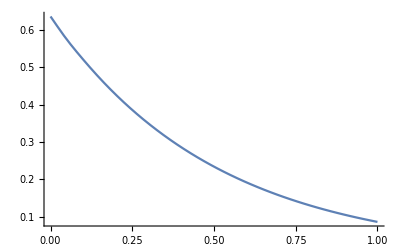

Calculating NL radius...

first function pass through sparse grid

now refining grid for spline

amount of data in spline: 85

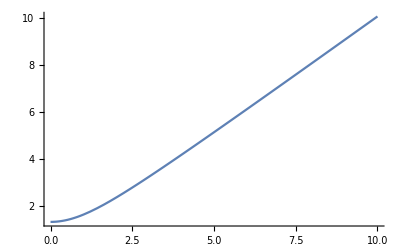

CALCULATING WxcNLR via the vxcNLR direct-density piece

first function pass through sparse grid

now refining grid for spline

amount of data in spline: 89

-0.863988

CALCULATING WxcNLR via the vxcNLR back-density piece...

first function pass through sparse grid

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {19.9827}. NIntegrate obtained -7.8938×10^-17 and 1.13461×10^-22 for the integral and error estimates.

now refining grid for spline

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {17.5802}. NIntegrate obtained 1.63555×10^-16 and 1.03606×10^-21 for the integral and error estimates.

amount of data in spline: 117

-0.863988

CALCULATING vxcNLR...

first function pass through sparse grid

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {19.9827}. NIntegrate obtained -7.8938×10^-17 and 1.13461×10^-22 for the integral and error estimates.

now refining grid for spline

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {17.5802}. NIntegrate obtained 1.63555×10^-16 and 1.03606×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {17.5802}. NIntegrate obtained 2.89855×10^-17 and 4.43236×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

amount of data in spline: 107

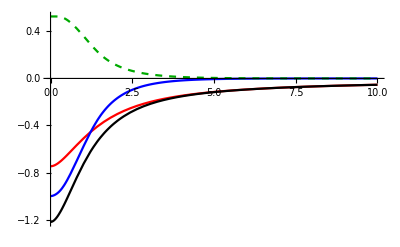

```mathematica
(* system properties *)
Z=1;
v[r_]:=-Z/r

soccupy={2}; (* how many electrons to put in each s orbital.  soccupy[[1]] is 1s, soccupy[[2]] is 2s, etc. *)
poccupy={}; (* how many electrons go in each p orbital.  everything is spherically averaged. *)
howmany=5; (* how many eigenfunctions to keep *)

(* grid properties *)
Ngrid=200; (* # of grid points *)
SPARSENgrid=25;  (* # of sparse grid points:  attempts to be this many grid points, but refines if necessary to achieve FUNCTIONtolerance.  Ideally dividing a multiple of two from Ngrid. *)
MAXr=40/Z; (* how far out to go in the grid *)
FOURTHorder=True;

(* tolerance to get FUNCTIONS to in BuildSpline, like Subscript[v, Hxc]^RNL(r) and Subscript[R, NL](r) *)
FUNCTIONtolerance=10*^-7;
(* Debug options *)
DEBUG=True;
SUPERdebug=False;

INIT (* initialize the grid *)
DIAG[v];  (* just diagonalize, don't run a self-consistent calculation *)
Plot[n[r],{r,0,1},PlotRange->All] (* try plotting the density *)

getRnl;
Plot[Rnl[r],{r,0,10},PlotRange->All]

getWxcNLR
getOtherWxcNLR
getvxcNLR;
vxcNLRbackR[r_]:=vxcNLR[r]-(vxcNLRdirect[r]+vxcNLRbackn[r])
Plot[{vxcNLRdirect[r],vxcNLRbackn[r],vxcNLRbackR[r],vxcNLR[r]},{r,0,10},PlotStyle->{{Red},{Blue},{Darker[Green],Dashed},{Black}},PlotRange->All]
```

# (* Lithium atom: self-consistent calculation *)

SetDelayed::write: Tag InterpolatingFunction in TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]] is Protected.

$Failed

KS-NLR calculation for Z = 3, s occupation = {2, 1}, p occupation = {}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {1.74065}. NIntegrate obtained 5.51812 and 5.58658×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {1.74065}. NIntegrate obtained 1.45876 and 1.96464×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rp near {rp} = {16.9968}. NIntegrate obtained -4.89091×10^-14 and 6.61035×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

KS-NLR converged in 12 iterations.

s eigenvalues = {-2.32924,-0.161653,-0.035341,-0.014341,0.000594325}

p eigenvalues = pHeig

Ts = 8.17011

V = -18.0373

WH = 4.33597

WxcNLR = -2.63897

EvNLR = -8.17016

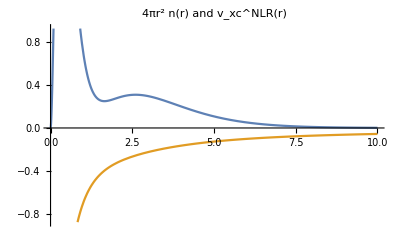

```mathematica
Z=3; (* charge of nucleus *)
v[r_]:=-Z/r ;(* external potential *)
soccupy={2,1}; (* how many electrons to put in each s orbital.  soccupy[[1]] is 1s, soccupy[[2]] is 2s, etc. *)
poccupy={}; (* how many electrons go in each p orbital.  everything is spherically averaged. *)
howmany=5; (* how many eigenfunctions to keep *)

(* grid properties *)
INITIALNgrid=80; (* since we run a self-consistent loop, start with lower accuracy *)
FINALNgrid=420; (* and work your way up *)
MAXr=42; (* largest distance out *)
FOURTHorder=True;

(* tolerance to get FUNCTIONS to in BuildSpline, like Subscript[v, Hxc]^RNL(r) and Subscript[R, NL](r) *)
INITIALfunctionTOLERANCE=10*^-4; (* start small *)
FINALfunctionTOLERANCE=10*^-6; (* work to greater accuracy later on *)

(* Debug options *)
DEBUG=False;
SUPERdebug=False;

(* KS convergence properties *)
KSenergytolerance=10*^-5; (* can stop grid refinement if energy stops changing past this decimal... *)
KSdensitytolerance=10*^-7; (* how to determine convergence in the density *)
KSlambda=0.8; (* how big a step to take each iteration.  should be greater than 0, and ≤ 1 *)
KSitermax=30; (* max iterations of the KS scheme *)

(* Every self-consistent calculation needs a starting density guess *)
n[r_]:=Z^3/Pi Exp[-2 Z r]+(Z/2)^3/Pi Exp[-2 (Z/2) r]+(Z/3)^3 /Pi Exp[-2 (Z/3)r]

(* KSNLR will take care of initiating the grid each iteration *)
KSNLR
```

```mathematica
(* CONVERGED LITHIUM QUANTITIES *)
(* These are the quantities you should get, roughly speaking. *)

n=Interpolation[{{0,15.341151514346231},{0.00008284600389863547,15.333539766979221},{0.011654850761193911,14.305334861665617},{0.03471601427188583,12.459688787666304},{0.06926633653597439,10.135184609220232},{0.11530581755345956,7.704575809898833},{0.17283445732434138,5.478796550789142},{0.24185225584861988,3.649738642762259},{0.322359213126295,2.2820777647886135},{0.4143553291573667,1.342696194863727},{0.5178406039418352,0.7455621835539568},{0.6328150374797002,0.392040576116269},{0.7592786297709618,0.1961751936722405},{0.8972313808156201,0.09436039726191667},{1.046673290613675,0.04469372136222273},{1.2076043591651267,0.021986687888758016},{1.3800245864699747,0.012245112725296404},{1.5639339725282198,0.008247250822996434},{1.7593325173398613,0.006539973534652159},{1.9662202209048996,0.005614033056500674},{2.184597083223334,0.004888939060050156},{2.414463104295166,0.004189990070664949},{2.6558182841203934,0.0034981557870670623},{2.9086626226990187,0.00284000767290821},{3.1729961200310397,0.0022446456671783572},{3.448818776116458,0.0017304090530069103},{3.736130590955272,0.0013036135682809751},{4.034931564547483,0.0009613406958235644},{4.345221696893091,0.0006949436653020966},{4.667000987992096,0.0004930340551790499},{5.000269437844498,0.0003436228022677789},{5.345027046450294,0.00023545837917359413},{5.70127381380949,0.0001587312711883642},{6.06900973992208,0.00010533346810249066},{6.448234824788068,0.00006883735508102298},{6.838949068407453,0.00004432005228831857},{7.241152470780234,0.00002812100736126501},{7.654845031906412,0.00001758850168185602},{8.080026751785985,0.000010846449740789},{8.516697630418957,6.596058607038283*^-6},{8.964857667805324,3.956248446401264*^-6},{9.424506863945089,2.340656967910114*^-6},{9.895645218838249,1.3661270014276656*^-6},{10.378272732484808,7.86647050399331*^-7},{10.872389404884762,4.469249505366658*^-7},{11.377995236038112,2.505419030746749*^-7},{11.895090225944859,1.3859205614985134*^-7},{12.423674374605003,7.565300857987578*^-8},{12.963747682018544,4.075293399608248*^-8},{13.515310148185481,2.1664515698804584*^-8},{14.078361773105815,1.1365989161973487*^-8},{14.652902556779546,5.884950257404521*^-9},{15.238932499206674,3.0072083626407817*^-9},{15.836451600387198,1.5166179345106553*^-9},{16.44545986032112,7.548952077762064*^-10},{17.065957279008437,3.708515272150983*^-10},{17.69794385644915,1.7981290586784976*^-10},{18.34141959264326,8.605040972537315*^-11},{18.996384487590763,4.064431046314932*^-11},{19.66283854129167,1.8948042234012023*^-11},{20.34078175374597,8.718652603340865*^-12},{21.030214124953666,3.959653831133156*^-12},{21.73113565491476,1.7749657827057404*^-12},{22.44354634362925,7.853252020220177*^-13},{23.167446191097138,3.4295530409029827*^-13},{23.90283519731842,1.4782756490094943*^-13},{24.649713362293102,6.28933224580614*^-14},{25.40808068602118,2.6411071761657928*^-14},{26.177937168502652,1.094714600674535*^-14},{26.959282809737523,4.47868056923988*^-15},{27.75211760972579,1.8085659641470276*^-15},{28.556441568467452,7.208656611439906*^-16},{29.372254685962513,2.836028031311695*^-16},{30.19955696221097,1.1012934074211296*^-16},{31.038348397212825,4.2211560644783956*^-17},{31.88862899096807,1.5969584185842237*^-17},{32.75039874347672,5.963254393496871*^-18},{33.623657654738764,2.1977765264180707*^-18},{34.508405724754205,7.99371696652012*^-19},{35.404642953523044,2.8685058880241404*^-19},{36.312369341045276,1.0178794908791353*^-19},{37.231584887320906,-7.765527712627521*^-23},{38.16228959234993,-3.33077479606927*^-25},{39.10448345613235,-1.3387880815882558*^-27},{40.05816647866817,-4.7813543624156736*^-30},{41.02333865995738,-1.2806852283430335*^-32},{42.,6.235419283480209*^-45}}];
vxcNLR=Interpolation[{{0,-3.480920638340791},{0.00008284600389863547,-3.4809183527901433},{0.011654850761193911,-3.4768501876341515},{0.03471601427188583,-3.447280259530708},{0.06926633653597439,-3.3602342599271022},{0.11530581755345956,-3.1888977378636714},{0.17283445732434138,-2.9249454044136334},{0.24185225584861988,-2.5841502719964584},{0.322359213126295,-2.2019727637676185},{0.4143553291573667,-1.8219772315274807},{0.5178406039418352,-1.481589702112368},{0.6328150374797002,-1.1987056009698427},{0.7592786297709618,-0.972901065342971},{0.8972313808156201,-0.7969742141524302},{1.046673290613675,-0.6620526537481441},{1.2076043591651267,-0.559387282826464},{1.3800245864699747,-0.4811754232023321},{1.5639339725282198,-0.42093750477660336},{1.7593325173398613,-0.3735970424288834},{1.9662202209048996,-0.33536956790831424},{2.184597083223334,-0.3035535195298917},{2.414463104295166,-0.2762933702844289},{2.6558182841203934,-0.2523599447147824},{2.9086626226990187,-0.23096432391182334},{3.1729961200310397,-0.21161381158115333},{3.448818776116458,-0.19400494860680936},{3.736130590955272,-0.17794776279189875},{4.034931564547483,-0.1633151179568817},{4.345221696893091,-0.1500103658303939},{4.667000987992096,-0.13794843981711463},{5.000269437844498,-0.1270460740408667},{5.345027046450294,-0.11721791857640294},{5.70127381380949,-0.10837614740539743},{6.06900973992208,-0.10043186679401199},{6.448234824788068,-0.09329720394217843},{6.838949068407453,-0.08688739521723192},{7.241152470780234,-0.08112251195555396},{7.654845031906412,-0.07592867843699322},{8.080026751785985,-0.07123877367657307},{8.516697630418957,-0.06699266947254791},{8.964857667805324,-0.06313713883958996},{9.424506863945089,-0.0596254767430615},{9.895645218838249,-0.05641698706584943},{10.378272732484808,-0.053476378504647606},{10.872389404884762,-0.05077313420156129},{11.377995236038112,-0.04828089998304523},{11.895090225944859,-0.04597691213429163},{12.423674374605003,-0.043841480933596765},{12.963747682018544,-0.04185753505732667},{13.515310148185481,-0.040010226910757146},{14.078361773105815,-0.03828659533432065},{14.652902556779546,-0.036675280196560835},{15.238932499206674,-0.03516628256823866},{15.836451600387198,-0.033750764092215946},{16.44545986032112,-0.03242087952736462},{17.065957279008437,-0.0311696370432495},{17.69794385644915,-0.029990781543039594},{18.34141959264326,-0.028878696940063474},{18.996384487590763,-0.027828324149313886},{19.66283854129167,-0.026835091777813465},{20.34078175374597,-0.02589485744773393},{21.030214124953666,-0.02500385777240117},{21.73113565491476,-0.024158665490401257},{22.44354634362925,-0.023356152558515073},{23.167446191097138,-0.022593458195718733},{23.90283519731842,-0.021867961081630936},{24.649713362293102,-0.02117725505597033},{25.40808068602118,-0.020519127786263577},{26.177937168502652,-0.01989154196671521},{26.959282809737523,-0.019292618687676056},{27.75211760972579,-0.018720622676399044},{28.556441568467452,-0.018173949159114945},{29.372254685962513,-0.017651112134287186},{30.19955696221097,-0.017150733879295478},{31.038348397212825,-0.01667153553930316},{31.88862899096807,-0.016212328668875828},{32.75039874347672,-0.015772007615009465},{33.623657654738764,-0.015349542645329891},{34.508405724754205,-0.014943973737928733},{35.404642953523044,-0.0145544049600281},{36.312369341045276,-0.014179999371806072},{37.231584887320906,-0.013819974399531748},{38.16228959234993,-0.013473597628869235},{39.10448345613235,-0.013140182975009268},{40.05816647866817,-0.012819087191317566},{41.02333865995738,-0.01250970668255046},{42.,-0.01221147459250648}}];
vH=Interpolation[{{0,6.01242521518003},{0.00008284600389863547,6.012424994708792},{0.011654850761193911,6.008210145430318},{0.03471601427188583,5.977491295535462},{0.06926633653597439,5.8866153367542084},{0.11530581755345956,5.706284243178384},{0.17283445732434138,5.424422092941848},{0.24185225584861988,5.0507593973668685},{0.322359213126295,4.6125873369707735},{0.4143553291573667,4.145288814914215},{0.5178406039418352,3.6825842209556563},{0.6328150374797002,3.2500239076400925},{0.7592786297709618,2.8627296378629934},{0.8972313808156201,2.526410120440448},{1.046673290613675,2.2399812351110318},{1.2076043591651267,1.9984064639630832},{1.3800245864699747,1.7949932697554098},{1.5639339725282198,1.62291648930773},{1.7593325173398613,1.4760466311565659},{1.9662202209048996,1.3492807248674494},{2.184597083223334,1.238573419854507},{2.414463104295166,1.1408183193796098},{2.6558182841203934,1.0536750481764896},{2.9086626226990187,0.97539434315904},{3.1729961200310397,0.9046651212273473},{3.448818776116458,0.8404912949535287},{3.736130590955272,0.7820979604832852},{4.034931564547483,0.728863077520002},{4.345221696893091,0.6802696836108987},{4.667000987992096,0.6358737750099306},{5.000269437844498,0.5952835861679139},{5.345027046450294,0.558146777834361},{5.70127381380949,0.5241428324898316},{6.06900973992208,0.49297867071315815},{6.448234824788068,0.46438610364160193},{6.838949068407453,0.43812021281930563},{7.241152470780234,0.41395810457463184},{7.654845031906412,0.39169773679040876},{8.080026751785985,0.37115668131557683},{8.516697630418957,0.352170785780082},{8.964857667805324,0.3345927528550139},{9.424506863945089,0.318290678547294},{9.895645218838249,0.303146595892425},{10.378272732484808,0.2890550650157018},{10.872389404884762,0.27592184073170606},{11.377995236038112,0.2636626381821544},{11.895090225944859,0.2522020074022112},{12.423674374605003,0.24147232000247185},{12.963747682018544,0.23141286553843854},{13.515310148185481,0.22196905142669915},{14.078361773105815,0.21309169811027007},{14.652902556779546,0.20473642019056407},{15.238932499206674,0.1968630840774941},{15.836451600387198,0.1894353330714062},{16.44545986032112,0.18242017145899023},{17.065957279008437,0.17578760002174604},{17.69794385644915,0.1695102962141378},{18.34141959264326,0.16356333310360316},{18.996384487590763,0.1579239319392286},{19.66283854129167,0.1525712439128336},{20.34078175374597,0.14748615729050865},{21.030214124953666,0.14265112662675747},{21.73113565491476,0.1380500212336304},{22.44354634362925,0.1336679904716113},{23.167446191097138,0.12949134376591478},{23.90283519731842,0.12550744353924434},{24.649713362293102,0.12170460949719877},{25.40808068602118,0.11807203291177074},{26.177937168502652,0.11459969972723279},{26.959282809737523,0.11127832146584021},{27.75211760972579,0.10809927304213512},{28.556441568467452,0.10505453670754743},{29.372254685962513,0.10213665144424082},{30.19955696221097,0.09933866721109799},{31.038348397212825,0.09665410351734713},{31.88862899096807,0.09407691186226282},{32.75039874347672,0.09160144163402734},{33.623657654738764,0.08922240910839462},{34.508405724754205,0.08693486922925864},{35.404642953523044,0.08473418988944174},{36.312369341045276,0.08261602846170409},{37.231584887320906,0.08057631035775063},{38.16228959234993,0.0786112094174006},{39.10448345613235,0.07671712995153374},{40.05816647866817,0.07489069028132533},{41.02333865995738,0.07312870763295459},{42.,0.0714281842617073}}];
vxcNLRdirect=Interpolation[{{0,-2.1260612366150684},{0.00008284600389863547,-2.126061133146376},{0.011654850761193911,-2.1240875863463193},{0.03471601427188583,-2.1097793541457053},{0.06926633653597439,-2.067836792148846},{0.11530581755345956,-1.9857241551743914},{0.17283445732434138,-1.8596902000585118},{0.24185225584861988,-1.6963446408235698},{0.322359213126295,-1.509740425877544},{0.4143553291573667,-1.3162561693266206},{0.5178406039418352,-1.130104573075681},{0.6328150374797002,-0.9610225994997117},{0.7592786297709618,-0.8140314307401016},{0.8972313808156201,-0.6903511055953901},{1.046673290613675,-0.5886543369563462},{1.2076043591651267,-0.5062179800973855},{1.3800245864699747,-0.4398003028616473},{1.5639339725282198,-0.38621542144655757},{1.7593325173398613,-0.3426460387428879},{1.9662202209048996,-0.3067665231156797},{2.184597083223334,-0.27674843927908777},{2.414463104295166,-0.25120526311681834},{2.6558182841203934,-0.22911383946434644},{2.9086626226990187,-0.20973399986210992},{3.1729961200310397,-0.19253678951205344},{3.448818776116458,-0.17714525659101235},{3.736130590955272,-0.1632882564034784},{4.034931564547483,-0.15076604057101947},{4.345221696893091,-0.1394257199724174},{4.667000987992096,-0.12914453832709025},{5.000269437844498,-0.11981901876350987},{5.345027046450294,-0.11135830936905587},{5.70127381380949,-0.10368037214398221},{6.06900973992208,-0.09670997980746746},{6.448234824788068,-0.09037777371703411},{6.838949068407453,-0.08461987661913722},{7.241152470780234,-0.07937774076470491},{7.654845031906412,-0.07459804789528918},{8.080026751785985,-0.0702325701299915},{8.516697630418957,-0.06623795908112917},{8.964857667805324,-0.06257546373677005},{9.424506863945089,-0.05921059373654193},{9.895645218838249,-0.056112749965512375},{10.378272732484808,-0.05325484355789463},{10.872389404884762,-0.05061292062037186},{11.377995236038112,-0.048165805258433905},{11.895090225944859,-0.045894768955653815},{12.423674374605003,-0.043783230560910665},{12.963747682018544,-0.041816488256243414},{13.515310148185481,-0.03998148287186991},{14.078361773105815,-0.038266590648280155},{14.652902556779546,-0.03666144284959787},{15.238932499206674,-0.03515676934577976},{15.836451600387198,-0.033744263266964475},{16.44545986032112,-0.03241646398511033},{17.065957279008437,-0.0311666559192285},{17.69794385644915,-0.02998878093868766},{18.34141959264326,-0.028877362421239786},{18.996384487590763,-0.02782743928927063},{19.66283854129167,-0.026834508589613646},{20.34078175374597,-0.02589447539531224},{21.030214124953666,-0.025003608991965062},{21.73113565491476,-0.024158504468686667},{22.44354634362925,-0.023356048967087668},{23.167446191097138,-0.022593391954196372},{23.90283519731842,-0.021867918979921002},{24.649713362293102,-0.021177228459263918},{25.40808068602118,-0.020519111086496466},{26.177937168502652,-0.019891531544905083},{26.959282809737523,-0.019292612223370184},{27.75211760972579,-0.0187206186912689},{28.556441568467452,-0.018173946717366284},{29.372254685962513,-0.017651110647347645},{30.19955696221097,-0.017150732979351},{31.038348397212825,-0.016671534997970236},{31.88862899096807,-0.01621232834525545},{32.75039874347672,-0.015772007422732857},{33.623657654738764,-0.015349542531794108},{34.508405724754205,-0.014943973671301543},{35.404642953523044,-0.014554404921170187},{36.312369341045276,-0.014179999349283734},{37.231584887320906,-0.013819974386558449},{38.16228959234993,-0.013473597621442679},{39.10448345613235,-0.013140182970784313},{40.05816647866817,-0.012819087188928916},{41.02333865995738,-0.0125097066812084},{42.,-0.012211474591757135}}];

(* END LITHIUM QUANTITIES *)
```